```mathematica
dmkpluspi00pfunct[m_,ep_]:=493/Sqrt[(m/2)^2-493^2]*(InterpolatingFunction[…][m/(2*493)*ep*(1+Sqrt[1-(2*493/m)^2])]-InterpolatingFunction[…][m/(2*493)*ep*(1-Sqrt[1-(2*493/m)^2])])
```

```mathematica
dmkpluspi2body0pfunct[m_,ep_]:=493/Sqrt[(m/2)^2-493^2]*(InterpolatingFunction[…][m/(2*493)*ep*(1+Sqrt[1-(2*493/m)^2])]-InterpolatingFunction[…][m/(2*493)*ep*(1-Sqrt[1-(2*493/m)^2])])
```

```mathematica
dmkplusleptefunct[m_,ep_]:=493/Sqrt[(m/2)^2-493^2]*(InterpolatingFunction[…][m/(2*493)*ep*(1+Sqrt[1-(2*493/m)^2])]-InterpolatingFunction[…][m/(2*493)*ep*(1-Sqrt[1-(2*493/m)^2])])
```

```mathematica
dmkplusleptmufunct[m_,ep_]:=493/Sqrt[(m/2)^2-493^2]*(InterpolatingFunction[…][m/(2*493)*ep*(1+Sqrt[1-(2*493/m)^2])]-InterpolatingFunction[…][m/(2*493)*ep*(1-Sqrt[1-(2*493/m)^2])])
```

```mathematica
normfunc[dmm_,f_,ep_]:=NIntegrate[(f),{ep,0,dmm}]
```

```mathematica
dmkpluspi00pnorma[dmm_,ep_]:=(((4*0.017)/Quiet[normfunc[dmm,dmkpluspi00pfunct[dmm,ep],ep]])*dmkpluspi00pfunct[dmm,ep])
```

```mathematica
dmkpluspi2body0pnorma[dmm_,ep_]:=(((2*0.207)/Quiet[normfunc[dmm,dmkpluspi2body0pfunct[dmm,ep],ep]])*dmkpluspi2body0pfunct[dmm,ep])
```

```mathematica
dmkplusleptenorma[dmm_,ep_]:=(((2*0.05)/Quiet[normfunc[dmm,dmkplusleptefunct[dmm,ep],ep]])*dmkplusleptefunct[dmm,ep])
```

```mathematica
dmkplusleptmunorma[dmm_,ep_]:=(((2*0.034)/Quiet[normfunc[dmm,dmkplusleptmufunct[dmm,ep],ep]])*dmkplusleptmufunct[dmm,ep])
```

```mathematica
kplusminus[m_,emax_]:=Quiet[Plot[{Evaluate[dmkpluspi00pnorma[m,ep]],Evaluate[dmkpluspi2body0pnorma[m,ep]],Evaluate[dmkplusleptenorma[m,ep]],Evaluate[dmkplusleptmunorma[m,ep]],Evaluate[dmkpluspi00pnorma[m,ep]+dmkpluspi2body0pnorma[m,ep]+dmkplusleptenorma[m,ep]+dmkplusleptmunorma[m,ep]]},{ep,0,emax},PlotRange->Full,PlotStyle->  {Red,Blue,Green,Magenta,Black},PlotLegends->{"K+ -> π+π0π0","K+ -> π+π0","K+ -> e ν π0","K+ -> μ ν π0","1/2 Total K+ K-"},PlotLabel->m "MeV Dark Matter -> K+ K- Photon Spectrum" ]]
```

```mathematica
justtotalpm[m_]:=Quiet[Plot[Evaluate[dmkpluspi00pnorma[m,ep]+dmkpluspi2body0pnorma[m,ep]+dmkplusleptenorma[m,ep]+dmkplusleptmunorma[m,ep]],{ep,0,m},PlotRange->Full,PlotLegends-> {m "MeV"},PlotStyle->RandomColor[]]]
```

```mathematica
totalspreadpm[mlist_,x_]:=Show[(justtotalpm[#])&/@mlist,PlotRange-> {{0,x},Full}]
```

```mathematica
kfile[m_,ep_] :=
Evaluate[dmkpluspi00pnorma[1100,ep]+dmkpluspi2body0pnorma[1100,ep]+dmkplusleptenorma[1100,ep]+dmkplusleptmunorma[1100,ep]]
```

```mathematica
elist=N@Subdivide[0.01,370,200]
dataset={elist,kfile[1100, elist]}
SetDirectory@NotebookDirectory[]
Export["K+- PDFs\sdfg.csv",dataset, "CSV"]
```

{0.01,1.85995,3.7099,5.55985,7.4098,9.25975,11.1097,12.9597,14.8096,16.6596,18.5095,20.3595,22.2094,24.0594,25.9093,27.7593,29.6092,31.4592,33.3091,35.1591,37.009,38.859,40.7089,42.5589,44.4088,46.2588,48.1087,49.9587,51.8086,53.6586,55.5085,57.3585,59.2084,61.0584,62.9083,64.7583,66.6082,68.4582,70.3081,72.1581,74.008,75.858,77.7079,79.5579,81.4078,83.2578,85.1077,86.9577,88.8076,90.6575,92.5075,94.3575,96.2074,98.0574,99.9073,101.757,103.607,105.457,107.307,109.157,111.007,112.857,114.707,116.557,118.407,120.257,122.107,123.957,125.807,127.657,129.507,131.356,133.206,135.056,136.906,138.756,140.606,142.456,144.306,146.156,148.006,149.856,151.706,153.556,155.406,157.256,159.106,160.956,162.806,164.656,166.506,168.355,170.205,172.055,173.905,175.755,177.605,179.455,181.305,183.155,185.005,186.855,188.705,190.555,192.405,194.255,196.105,197.955,199.805,201.655,203.505,205.354,207.204,209.054,210.904,212.754,214.604,216.454,218.304,220.154,222.004,223.854,225.704,227.554,229.404,231.254,233.104,234.954,236.804,238.654,240.504,242.353,244.203,246.053,247.903,249.753,251.603,253.453,255.303,257.153,259.003,260.853,262.703,264.553,266.403,268.253,270.103,271.953,273.803,275.653,277.503,279.352,281.202,283.052,284.902,286.752,288.602,290.452,292.302,294.152,296.002,297.852,299.702,301.552,303.402,305.252,307.102,308.952,310.802,312.652,314.502,316.351,318.201,320.051,321.901,323.751,325.601,327.451,329.301,331.151,333.001,334.851,336.701,338.551,340.401,342.251,344.101,345.951,347.801,349.651,351.501,353.35,355.2,357.05,358.9,360.75,362.6,364.45,366.3,368.15,370.}

InterpolatingFunction::dmval: Input value {179.234} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180.383} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {181.532} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.01,1.85995,3.7099,5.55985,7.4098,9.25975,11.1097,12.9597,14.8096,16.6596,18.5095,20.3595,22.2094,24.0594,25.9093,27.7593,29.6092,31.4592,33.3091,35.1591,37.009,38.859,40.7089,42.5589,44.4088,46.2588,48.1087,49.9587,51.8086,53.6586,55.5085,57.3585,59.2084,61.0584,62.9083,64.7583,66.6082,68.4582,70.3081,72.1581,74.008,75.858,77.7079,79.5579,81.4078,83.2578,85.1077,86.9577,88.8076,90.6575,92.5075,94.3575,96.2074,98.0574,99.9073,101.757,103.607,105.457,107.307,109.157,111.007,112.857,114.707,116.557,118.407,120.257,122.107,123.957,125.807,127.657,129.507,131.356,133.206,135.056,136.906,138.756,140.606,142.456,144.306,146.156,148.006,149.856,151.706,153.556,155.406,157.256,159.106,160.956,162.806,164.656,166.506,168.355,170.205,172.055,173.905,175.755,177.605,179.455,181.305,183.155,185.005,186.855,188.705,190.555,192.405,194.255,196.105,197.955,199.805,201.655,203.505,205.354,207.204,209.054,210.904,212.754,214.604,216.454,218.304,220.154,222.004,223.854,225.704,227.554,229.404,231.254,233.104,234.954,236.804,238.654,240.504,242.353,244.203,246.053,247.903,249.753,251.603,253.453,255.303,257.153,259.003,260.853,262.703,264.553,266.403,268.253,270.103,271.953,273.803,275.653,277.503,279.352,281.202,283.052,284.902,286.752,288.602,290.452,292.302,294.152,296.002,297.852,299.702,301.552,303.402,305.252,307.102,308.952,310.802,312.652,314.502,316.351,318.201,320.051,321.901,323.751,325.601,327.451,329.301,331.151,333.001,334.851,336.701,338.551,340.401,342.251,344.101,345.951,347.801,349.651,351.501,353.35,355.2,357.05,358.9,360.75,362.6,364.45,366.3,368.15,370.},{0.,0.,0.,0.,0.,0.,-1.41138×10^-11,0.0000360441,0.000313707,0.000569246,0.000831699,0.00112365,0.0014182,0.00170994,0.00199485,0.0022705,0.00253563,0.00279258,0.00300739,0.00313771,0.0032509,0.00335997,0.00346272,0.00355936,0.0036502,0.00373137,0.0037904,0.0038416,0.00388522,0.00392189,0.00395223,0.00397687,0.00399633,0.00401113,0.00402169,0.0040284,0.00403158,0.00403154,0.00402852,0.00402275,0.00401442,0.00400372,0.0039908,0.0039758,0.00395887,0.00394011,0.00391964,0.00389759,0.00387406,0.00384915,0.00382299,0.00379569,0.00376737,0.00373818,0.00370738,0.00366898,0.00363099,0.00359333,0.00355601,0.00351903,0.00348242,0.00344619,0.00341034,0.00337488,0.00333984,0.00330522,0.00327102,0.00323727,0.00320397,0.00317114,0.00313877,0.00310689,0.00307549,0.00304459,0.0030142,0.00298429,0.00294731,0.00289126,0.0028366,0.00278279,0.00272983,0.00267771,0.0026264,0.00257591,0.0025262,0.00247728,0.00242912,0.00238173,0.00233508,0.00228917,0.00224398,0.00219951,0.00215574,0.00211267,0.00207029,0.00202858,0.00198754,0.00194715,0.00190742,0.00186832,0.00182986,0.00179203,0.0017548,0.00171819,0.00168217,0.00164675,0.00161191,0.00157765,0.00154395,0.00151082,0.00147824,0.0014462,0.00141471,0.00138374,0.0013533,0.00132337,0.00129396,0.00126504,0.00123662,0.00120869,0.00118123,0.00115425,0.00112773,0.00110167,0.00107606,0.00105089,0.00102615,0.00100184,0.000977945,0.000954462,0.000931381,0.000908692,0.000886387,0.000864458,0.000842894,0.000821687,0.000800825,0.000780297,0.000760082,0.000740126,0.000721472,0.000705393,0.000689377,0.00067352,0.000657821,0.000642275,0.000626882,0.000611639,0.000596542,0.00058159,0.000566781,0.000552112,0.00053758,0.000523184,0.00050892,0.000494788,0.000480784,0.000466906,0.000453152,0.00043952,0.000426008,0.000412614,0.000399335,0.000386169,0.000373114,0.000360169,0.000347331,0.000334597,0.000321967,0.000309438,0.000297009,0.000284676,0.000272439,0.000260295,0.000248243,0.000236281,0.000224406,0.000212618,0.000200914,0.000189293,0.000177752,0.000166291,0.000154908,0.000143601,0.000132367,0.000121207,0.000110118,0.000099099,0.000088148,0.0000772639,0.0000664451,0.0000556902,0.0000449981,0.0000343672,0.0000237963,0.0000132397,2.93651×10^-6,-5.22708×10^-7,3.12186×10^-8,3.75793×10^-9,1.62393×10^-9}}

C:\Users\jacob\Desktop\EtaPion

K+- PDFs\sdfg.csv

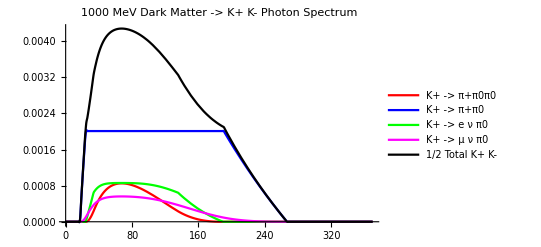

```mathematica
kplusminus[1000,370]
```

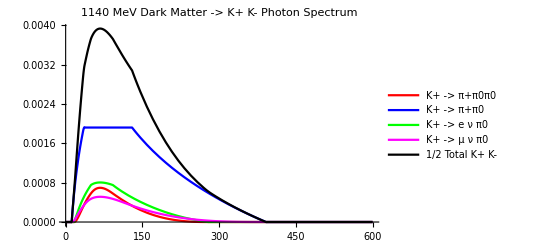

```mathematica
kplusminus[1140,600]
```

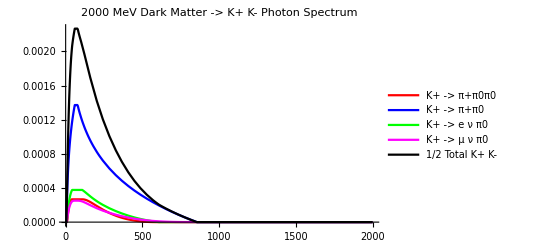

```mathematica
kplusminus[2000,2000]
```

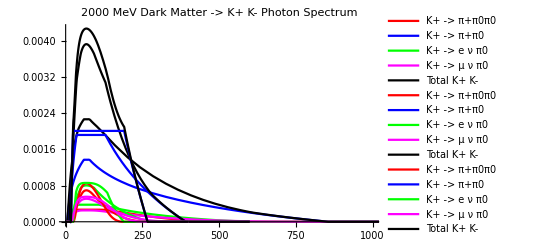

```mathematica
Show[{Out[752],Out[751],Out[750]}, PlotRange-> {{0,1000},Full}]
```

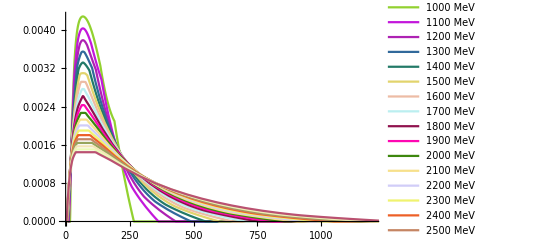

```mathematica
totalspreadpm[Table[1000+100*(i-1),{i,20}],1200]
```